```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/DESI/math

```mathematica
$Assumptions={f>0,V0>0,t>0,x0>0};
```

```mathematica
D[D[(V0 Tanh[x/f]^2), x], x]/.{x->0}
```

(2 V0)/f^2

```mathematica
Normal[Series[V0 Tanh[x/f]^(2n),{x,0,0}]]
```

V0 (x/f)^(2 n)

```mathematica
Solve[(6n)/(1+n)==3(1+w),w]
```

{{w→(-1+n)/(1+n)}}

### Eemeli

```mathematica
u1[t_]=(-Sin[(π t)/T])/Sqrt[U0/ρ-Sin[(π t)/T]^2];
u2[t_]=(-U0/ρ Cos[(π t)/T]+(π t)/T Sin[(π t)/T])/Sqrt[U0/ρ-Sin[(π t)/T]^2];
```

```mathematica
G=Simplify[{{u1[T],u2[T]},{u1'[T],u2'[T]}}/.{U0->ρ Tanh[x0]^2,T->(π Cosh[x0])/Sqrt[2]}]
```

{{0,Tanh[x0]},{√2 Csch[x0],-√2 π Csch[x0]}}

```mathematica
Simplify[Tr[G]/.{U0->ρ Tanh[x0]^2,T->(π Cosh[x0])/Sqrt[2]},{x0>0}]
```

-√2 π Csch[x0]

## H = 0

```mathematica
V[x_]=Tanh[x]^2;
```

```mathematica
dT=π/Sqrt[2(1-Tanh[x0]^2)]//Simplify
xsol[t_]=ArcSinh[Cos[(π t)/dT]/Sqrt[1/Tanh[x0]^2-1]]//Simplify
```

(π Cosh[x0])/(√2)

ArcSinh[Cos[√2 t Sech[x0]] Sinh[x0]]

```mathematica
xsol[0]//Simplify
xsol[dT]//Simplify
xsol'[0]
```

x0

-x0

0

```mathematica
Simplify[xsol''[t]+V'[xsol[t]]]
```

0

```mathematica
Vpp[t_]=V''[xsol[t]]//Simplify;
```

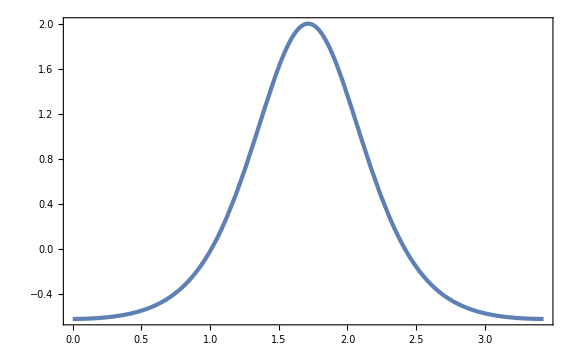

```mathematica
Plot[Vpp[t]/.{x0->1},{t,0,dT/.{x0->1}}]
```

```mathematica
VppMean=1/dT Integrate[Vpp[t],{t,0,dT}]//Simplify
```

Sech[x0] (-1+3 Sech[x0]^2)

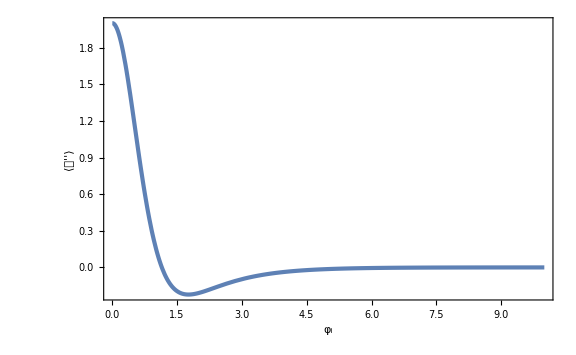

```mathematica
Plot[VppMean,{x0,0,10},PlotRange->Full,FrameLabel->{Subscript[φ, "i"],⟨𝒱''⟩}]
```

```mathematica
Integrate[(Vpp[t]-VppMean),{t,0,dT}]
```

0

```mathematica
VppVar=1/dT Integrate[Vpp[t]^2,{t,0,dT}]-VppMean^2//Simplify
```

1/8 (447+468 Cosh[x0]+92 Cosh[2 x0]+12 Cosh[3 x0]+5 Cosh[4 x0]) Sech[x0]^7 Sinh[x0/2]^4

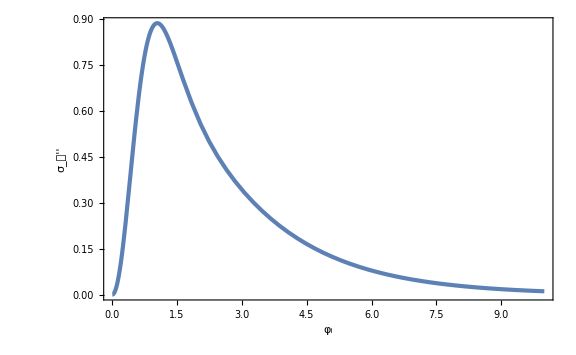

```mathematica
Plot[Sqrt[VppVar],{x0,0,10},FrameLabel->{Subscript[φ, "i"],Subscript[σ, 𝒱'']}]
```

```mathematica
psi[θ_]=-(Vpp[θ dT/π]-VppMean)/Sqrt[2VppVar]//Simplify;
```

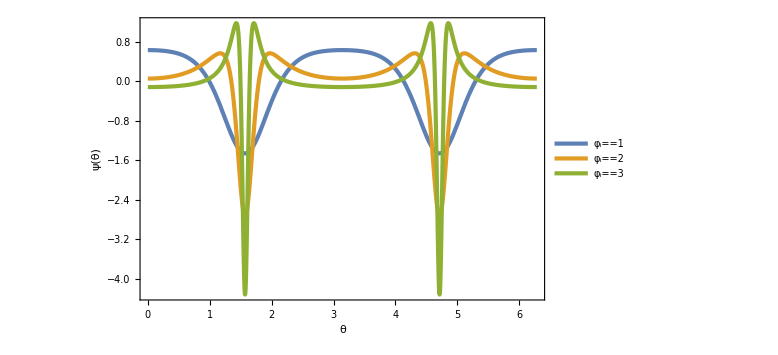

```mathematica
Plot[{psi[θ]/.{x0->1},psi[θ]/.{x0->2},psi[θ]/.{x0->3}},{θ,0,2π},PlotRange->Full,FrameLabel->{θ,ψ[θ]},PlotLegends->Placed[{Subscript[φ, "i"]==1,Subscript[φ, "i"]==2,Subscript[φ, "i"]==3},{0.5,0.3}]]
```

```mathematica
VppMean(dT/π)^2/.{x0->1.}
VppMean(dT/π)^2/.{x0->2.}
VppMean(dT/π)^2/.{x0->3.}
```

0.200541

-1.48239

-4.88484

```mathematica
Sqrt[VppVar/2](dT/π)^2/.{x0->1.}
Sqrt[VppVar/2](dT/π)^2/.{x0->2.}
Sqrt[VppVar/2](dT/π)^2/.{x0->3.}
```

0.745541

2.85789

12.2815

```mathematica
x0s=1;
FloquetList=Flatten[ParallelTable[u1sol=NDSolve[{u''[θ]+(Ak-2q psi[θ])u[θ]==0,u[0]==1,u'[0]==0}/.{x0->x0s},{u[θ],u'[θ]},{θ,0,π}][[1]];
u2sol=NDSolve[{u''[θ]+(Ak-2q psi[θ])u[θ]==0,u[0]==0,u'[0]==1}/.{x0->x0s},{u[θ],u'[θ]},{θ,0,π}][[1]];
w[θ_]=Transpose[{{u[θ],u'[θ]}/.u1sol,{u[θ],u'[θ]}/.u2sol}];
{Ak,q,Re[ArcCosh[1/2 Tr[w[π]]]]},{Ak,-8,15,5 10^-2},{q,-0,15,5 10^-2}],1];//AbsoluteTiming
FloquetFig=Show[ListDensityPlot[FloquetList,PlotLegends->BarLegend[Automatic,LegendLabel->Placed[Row[{Subscript[μ, κ],Δτ}],Right]],FrameLabel->{{q,None},{Subscript[A, κ],Subscript[φ, "i"]==x0s}}],Plot[Sqrt[VppVar/2](dT/π)^2/.{x0->x0s},{x,-8,15},PlotStyle->{Black,Dashed,AbsoluteThickness[3]}],
Plot[40(UnitStep[VppMean(dT/π)^2-x/.{x0->x0s}]-1/2),{x,-8,15},Filling->Bottom,FillingStyle->HatchFilling[],PlotStyle->Color[4],PlotRange->{{-8,15},{0,15}}]]
Export["Floquet_xi="<>ToString[x0s]<>".pdf",FloquetFig,ImageResolution->300];
```

{33.1395,Null}

-Graphics-

```mathematica
x0s=2;
FloquetList=Flatten[ParallelTable[u1sol=NDSolve[{u''[θ]+(Ak-2q psi[θ])u[θ]==0,u[0]==1,u'[0]==0}/.{x0->x0s},{u[θ],u'[θ]},{θ,0,π}][[1]];
u2sol=NDSolve[{u''[θ]+(Ak-2q psi[θ])u[θ]==0,u[0]==0,u'[0]==1}/.{x0->x0s},{u[θ],u'[θ]},{θ,0,π}][[1]];
w[θ_]=Transpose[{{u[θ],u'[θ]}/.u1sol,{u[θ],u'[θ]}/.u2sol}];
{Ak,q,Re[ArcCosh[1/2 Tr[w[π]]]]},{Ak,-8,15,5 10^-2},{q,-0,15,5 10^-2}],1];//AbsoluteTiming
FloquetFig=Show[ListDensityPlot[FloquetList,PlotLegends->BarLegend[Automatic,LegendLabel->Placed[Row[{Subscript[μ, κ],Δτ}],Right]],FrameLabel->{{q,None},{Subscript[A, κ],Subscript[φ, "i"]==x0s}}],Plot[Sqrt[VppVar/2](dT/π)^2/.{x0->x0s},{x,-8,15},PlotStyle->{Black,Dashed,AbsoluteThickness[3]}],
Plot[40(UnitStep[VppMean(dT/π)^2-x/.{x0->x0s}]-1/2),{x,-8,15},Filling->Bottom,FillingStyle->HatchFilling[],PlotStyle->Color[4],PlotRange->{{-8,15},{0,15}}]]
Export["Floquet_xi="<>ToString[x0s]<>".pdf",FloquetFig,ImageResolution->300];
```

{32.4844,Null}

-Graphics-

```mathematica
x0s=3;
FloquetList=Flatten[ParallelTable[u1sol=NDSolve[{u''[θ]+(Ak-2q psi[θ])u[θ]==0,u[0]==1,u'[0]==0}/.{x0->x0s},{u[θ],u'[θ]},{θ,0,π}][[1]];
u2sol=NDSolve[{u''[θ]+(Ak-2q psi[θ])u[θ]==0,u[0]==0,u'[0]==1}/.{x0->x0s},{u[θ],u'[θ]},{θ,0,π}][[1]];
w[θ_]=Transpose[{{u[θ],u'[θ]}/.u1sol,{u[θ],u'[θ]}/.u2sol}];
{Ak,q,Re[ArcCosh[1/2 Tr[w[π]]]]},{Ak,-8,15,5 10^-2},{q,-0,15,5 10^-2}],1];//AbsoluteTiming
FloquetFig=Show[ListDensityPlot[FloquetList,PlotLegends->BarLegend[Automatic,LegendLabel->Placed[Row[{Subscript[μ, κ],Δτ}],Right]],FrameLabel->{{q,None},{Subscript[A, κ],Subscript[φ, "i"]==x0s}}],Plot[Sqrt[VppVar/2](dT/π)^2/.{x0->x0s},{x,-8,15},PlotStyle->{Black,Dashed,AbsoluteThickness[3]}],
Plot[40(UnitStep[VppMean(dT/π)^2-x/.{x0->x0s}]-1/2),{x,-8,15},Filling->Bottom,FillingStyle->HatchFilling[],PlotStyle->Color[4],PlotRange->{{-8,15},{0,15}}]]
Export["Floquet_xi="<>ToString[x0s]<>".pdf",FloquetFig,ImageResolution->300];
```

{33.5933,Null}

-Graphics-

```mathematica
FloquetFunc=Flatten[ParallelTable[u1sol=NDSolve[{u''[θ]+(Ak-2q psi[θ])u[θ]==0,u[0]==1,u'[0]==0}/.{Ak->(k^2+VppMean)(dT/π)^2,q->Sqrt[VppVar/2](dT/π)^2},{u[θ],u'[θ]},{θ,0,π}][[1]];
u2sol=NDSolve[{u''[θ]+(Ak-2q psi[θ])u[θ]==0,u[0]==0,u'[0]==1}/.{Ak->(k^2+VppMean)(dT/π)^2,q->Sqrt[VppVar/2](dT/π)^2},{u[θ],u'[θ]},{θ,0,π}][[1]];
w[θ_]=Transpose[{{u[θ],u'[θ]}/.u1sol,{u[θ],u'[θ]}/.u2sol}];
{k,x0,Re[ArcCosh[1/2 Tr[w[π]]]]},{x0,10^-2,3,5 10^-3},{k,0,2.5,5 10^-3}],1];//AbsoluteTiming
```

{82.7912,Null}

```mathematica
Export["Floquet.csv",FloquetFunc//N];
```

```mathematica
FloquetFunc=Import["Floquet.csv"];
```

```mathematica
FloquetFuncFig=ListDensityPlot[FloquetFunc,FrameLabel->{κ,Subscript[φ, "i"]},PlotLegends->BarLegend[Automatic,LegendLabel->Placed[Row[{Subscript[μ, κ],Δτ}],Right]],PlotRange->Full]
```

-Graphics-

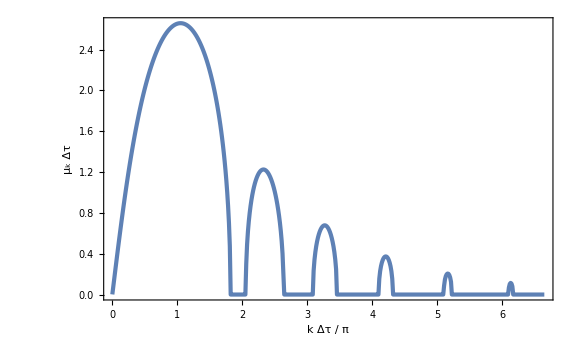

```mathematica
ListPlot[Map[{#[[1]]dT/π/.{x0->2},#[[3]]}&,Select[FloquetFunc,#[[2]]==2&]],PlotRange->Full,FrameLabel->{{Row[{Subscript[μ, k]," ",Δτ}],None},{Row[{k Δτ," / ",π}],Subscript[φ, "i"]==2}}]
```

## w/ matter

```mathematica
f=10^-3;
h=0.663;(*0.67;*)(*0.66;*)(*0.674;*)
Ωm=0.316;(*0.31*)(*0.32;*)(*0.3;*)
ρm0=3 h^2 Ωm;
V0=1.1 3(1-Ωm)h^2;
xi=7.32f;(*7.33f;*)
zi=9;(*1000;*)
mth=Sqrt[V0]/f
```

988.679

```mathematica
V[x_]=V0 Tanh[x/f]^2;
H[x_,p_,z_]=Sqrt[(p^2/2+V[x]+ρm0(1+z)^3)/3];
```

```mathematica
Hi=H[xi,0,zi];
tf=100/Hi;
```

```mathematica
txmax={};
txzero={};
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t],z[t]]x'[t]+V'[x[t]]==0,z'[t]==-(1+z[t])H[x[t],x'[t],z[t]],x[0]==xi,x'[0]==0,z[0]==zi,WhenEvent[x'[t]==0,AppendTo[txmax,t]],WhenEvent[x[t]==0,AppendTo[txzero,t]],WhenEvent[z[t]==0,t0=t]},{x[t],x'[t],z[t]},{t,0,tf},WorkingPrecision->30,MaxSteps->10^6][[1]];//AbsoluteTiming
```

NDSolve::precw: The precision of the differential equation ({{1954.97 Sech[Times[«2»]]^2 Tanh[1000 x[«1»]]+√3 x'[t] √(Times[«2»]+Times[«2»]+Times[«2»])+x''[t]==0,z'[t]==((-1-z[t]) √(0.977486 Power[«2»]+0.418176 Power[«2»]+1/2 Power[«2»]))/(√3),x[0]==0.00732,x'[0]==0,z[0]==9},{},{},{},{WhenEvent[x'[t]==0,AppendTo[txmax,t]],WhenEvent[x[t]==0,AppendTo[txzero,t]],WhenEvent[z[t]==0,t0=t]}}) is less than WorkingPrecision (30.).

{54.7905,Null}

```mathematica
xsol[t_]=x[t]/.bgsol;
psol[t_]=x'[t]/.bgsol;
zsol[t_]=z[t]/.bgsol;
Hsol[t_]=H[xsol[t],psol[t],zsol[t]];
wsol[t_]=(psol[t]^2/2-V[xsol[t]])/(psol[t]^2/2+V[xsol[t]]);
Vppsol[t_]=V''[xsol[t]];
dTList=Differences[txmax];
```

```mathematica
Hsol[t0]
ρm0/(3 Hsol[t0]^2)
t0 660
```

0.660707

0.319316

897.190041976350346470160076889

```mathematica
FloquetFunc=Import["Floquet.csv"];
```

```mathematica
padFP={{100,10},{70,50}};
```

```mathematica
FloquetFuncFig=Show[ListDensityPlot[FloquetFunc,FrameLabel->{"k / m_th","ϕ_(<i>) / f"},PlotLegends->BarLegend[Automatic,LegendLabel->Placed[Row[{Subscript[μ, k],Δτ}],Right]],PlotRange->Full,ImagePadding->padFP],
ListLinePlot[{Table[{1(1+zsol[txzero[[i+1]]]),(Abs[xsol[txmax[[i]]]]+Abs[xsol[txmax[[i+1]]]])/(2f)},{i,1,Length[txmax]-1}],
Table[{0.5(1+zsol[txzero[[i+1]]]),(Abs[xsol[txmax[[i]]]]+Abs[xsol[txmax[[i+1]]]])/(2f)},{i,1,Length[txmax]-1}],
Table[{1.5(1+zsol[txzero[[i+1]]]),(Abs[xsol[txmax[[i]]]]+Abs[xsol[txmax[[i+1]]]])/(2f)},{i,1,Length[txmax]-1}],
Table[{2(1+zsol[txzero[[i+1]]]),(Abs[xsol[txmax[[i]]]]+Abs[xsol[txmax[[i+1]]]])/(2f)},{i,1,Length[txmax]-1}],
Table[{2.5(1+zsol[txzero[[i+1]]]),(Abs[xsol[txmax[[i]]]]+Abs[xsol[txmax[[i+1]]]])/(2f)},{i,1,Length[txmax]-1}],
Table[{3.5(1+zsol[txzero[[i+1]]]),(Abs[xsol[txmax[[i]]]]+Abs[xsol[txmax[[i+1]]]])/(2f)},{i,1,Length[txmax]-1}]},PlotStyle->{{White,AbsoluteThickness[2]}},PlotRange->Full],
ListLinePlot[{Table[{0.5(1+zsol[txzero[[i+1]]]),(Abs[xsol[txmax[[i]]]]+Abs[xsol[txmax[[i+1]]]])/(2f)},{i,1,Length[txmax]/50}],Table[{1(1+zsol[txzero[[i+1]]]),(Abs[xsol[txmax[[i]]]]+Abs[xsol[txmax[[i+1]]]])/(2f)},{i,1,Length[txmax]/40}],
Table[{1.5(1+zsol[txzero[[i+1]]]),(Abs[xsol[txmax[[i]]]]+Abs[xsol[txmax[[i+1]]]])/(2f)},{i,1,Length[txmax]/30}],
Table[{2(1+zsol[txzero[[i+1]]]),(Abs[xsol[txmax[[i]]]]+Abs[xsol[txmax[[i+1]]]])/(2f)},{i,1,Length[txmax]/20}],
Table[{2.5(1+zsol[txzero[[i+1]]]),(Abs[xsol[txmax[[i]]]]+Abs[xsol[txmax[[i+1]]]])/(2f)},{i,1,Length[txmax]/15}],
Table[{3.5(1+zsol[txzero[[i+1]]]),(Abs[xsol[txmax[[i]]]]+Abs[xsol[txmax[[i+1]]]])/(2f)},{i,1,Length[txmax]/8}]},PlotStyle->{{White,AbsoluteThickness[2]}},PlotRange->Full]/.Line->Arrow]
```

-Graphics-

```mathematica
Export["Floquet.pdf",FloquetFuncFig,ImageResolution->300];
```

```mathematica
510,720
```

```mathematica
296,495
```

```mathematica
510/296 495//N
```

852.872

```mathematica
852/(852+720)0.95//N
```

0.514885

```mathematica
(1-852/(852+720))0.95//N
```

0.435115

```mathematica
tf=20/Hi;
txmax={};
txzero={};
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t],z[t]]x'[t]+V'[x[t]]==0,z'[t]==-(1+z[t])H[x[t],x'[t],z[t]],x[0]==xi,x'[0]==0,z[0]==zi,WhenEvent[x'[t]==0,AppendTo[txmax,t]],WhenEvent[x[t]==0,AppendTo[txzero,t]],WhenEvent[z[t]==0,t0=t]},{x[t],x'[t],z[t]},{t,0,tf},WorkingPrecision->30,MaxSteps->10^6][[1]];
```

NDSolve::precw: The precision of the differential equation ({{1954.97 Sech[Times[«2»]]^2 Tanh[1000 x[«1»]]+√3 x'[t] √(Times[«2»]+Times[«2»]+Times[«2»])+x''[t]==0,z'[t]==((-1-z[t]) √(0.977486 Power[«2»]+0.418176 Power[«2»]+1/2 Power[«2»]))/(√3),x[0]==0.00732,x'[0]==0,z[0]==9},{},{},{},{WhenEvent[x'[t]==0,AppendTo[txmax,t]],WhenEvent[x[t]==0,AppendTo[txzero,t]],WhenEvent[z[t]==0,t0=t]}}) is less than WorkingPrecision (30.).

```mathematica
xsol[t_]=x[t]/.bgsol;
psol[t_]=x'[t]/.bgsol;
zsol[t_]=z[t]/.bgsol;
Hsol[t_]=H[xsol[t],psol[t],zsol[t]];
wsol[t_]=(psol[t]^2/2-V[xsol[t]])/(psol[t]^2/2+V[xsol[t]]);
Vppsol[t_]=V''[xsol[t]];
dTList=Differences[txmax];
```

```mathematica
3 Hsol[t0]^2
V[xsol[t0]]+psol[t0]^2/2+ρm0
ρm0/(3 Hsol[t0]^2)
```

1.3096

1.3096

0.319316

```mathematica
VppMeanList=ParallelTable[1/dTList[[i]] NIntegrate[Vppsol[t]/mth^2,{t,txmax[[i]],txmax[[i+1]]}],{i,Length[dTList]}];//AbsoluteTiming
```

{74.56,Null}

```mathematica
VppVarList=ParallelTable[1/dTList[[i]] NIntegrate[Vppsol[t]^2/mth^4,{t,txmax[[i]],txmax[[i+1]]}]-VppMeanList[[i]]^2,{i,Length[dTList]}];//AbsoluteTiming
```

{43.9194,Null}

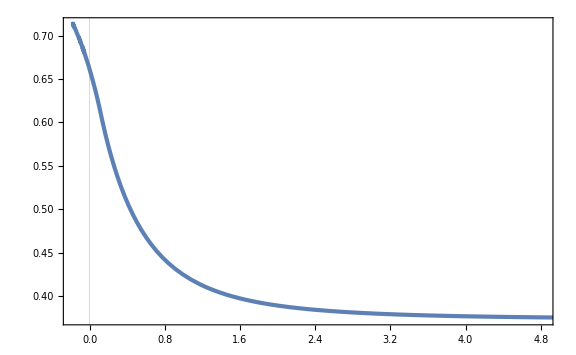

```mathematica
ParametricPlot[{zsol[t],(1+zsol[t])^(-3/2)Hsol[t]},{t,0,tf},GridLines->{{0},None}]
```

```mathematica
pad={{100,10},{70,10}};
```

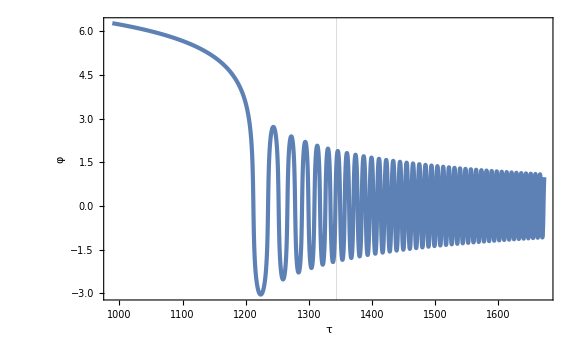

```mathematica
Plot[xsol[tp/mth]/f,{tp,mth,tf mth},PlotRange->Full,GridLines->{{mth t0},None},FrameLabel->{τ,φ},ImagePadding->pad,PlotPoints->200]
```

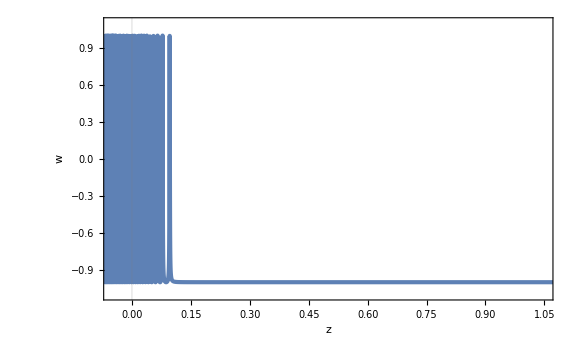

```mathematica
ParametricPlot[{zsol[t],wsol[t]},{t,0,tf},PlotRange->{{-0.05,1.05},{-1.1,1.1}},FrameLabel->{z,w},GridLines->{{0},None},ImagePadding->pad,PlotPoints->300]
```

```mathematica
pad={{100,10},{70,50}};
```

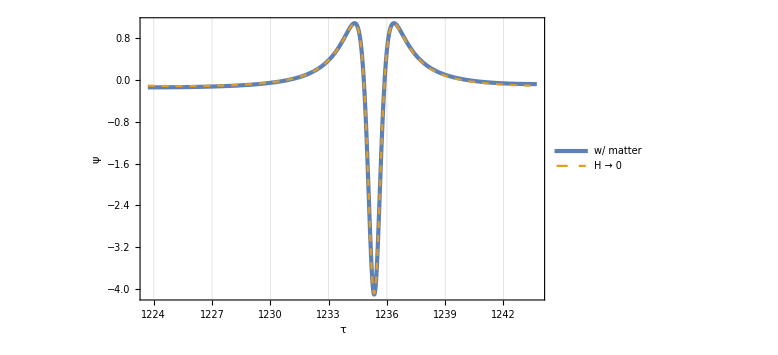

```mathematica
is=1;
Plot[{-(Vppsol[tp/mth]/mth^2-VppMeanList[[is]])/Sqrt[2VppVarList[[is]]],psi[π(tp-mth txzero[[is+1]]+1/2 dT)/dT]/.{x0->(Abs[xsol[txmax[[is]]]]+Abs[xsol[txmax[[is+1]]]])/(2f)}},{tp,mth txmax[[is]],mth txmax[[is+1]]},PlotRange->Full,GridLines->{txzero,None},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{ψ,None},{τ,n==is}},PlotLegends->Placed[{"w/ matter","H → 0"},{0.2,0.2}],ImagePadding->pad]
```

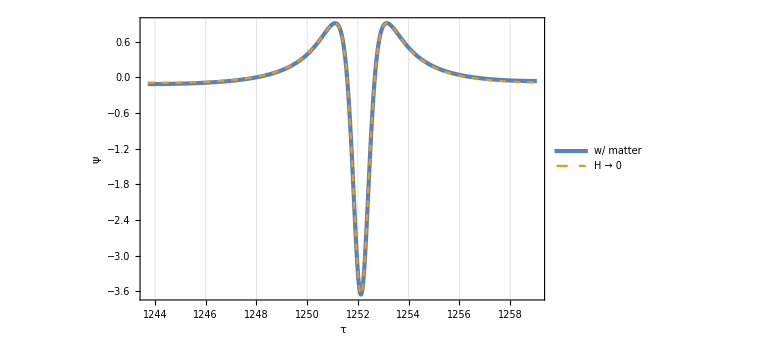

```mathematica
is=2;
Plot[{-(Vppsol[tp/mth]/mth^2-VppMeanList[[is]])/Sqrt[2VppVarList[[is]]],psi[π(tp-mth txzero[[is+1]]+1/2 dT)/dT]/.{x0->(Abs[xsol[txmax[[is]]]]+Abs[xsol[txmax[[is+1]]]])/(2f)}},{tp,mth txmax[[is]],mth txmax[[is+1]]},PlotRange->Full,GridLines->{txzero,None},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{ψ,None},{τ,n==is}},PlotLegends->Placed[{"w/ matter","H → 0"},{0.2,0.2}],ImagePadding->pad]
```

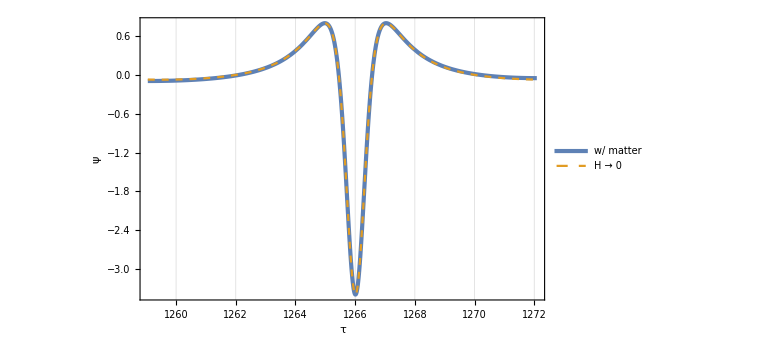

```mathematica
is=3;
Plot[{-(Vppsol[tp/mth]/mth^2-VppMeanList[[is]])/Sqrt[2VppVarList[[is]]],psi[π(tp-mth txzero[[is+1]]+1/2 dT)/dT]/.{x0->(Abs[xsol[txmax[[is]]]]+Abs[xsol[txmax[[is+1]]]])/(2f)}},{tp,mth txmax[[is]],mth txmax[[is+1]]},PlotRange->Full,GridLines->{txzero,None},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{ψ,None},{τ,n==is}},PlotLegends->Placed[{"w/ matter","H → 0"},{0.2,0.2}],ImagePadding->pad]
```

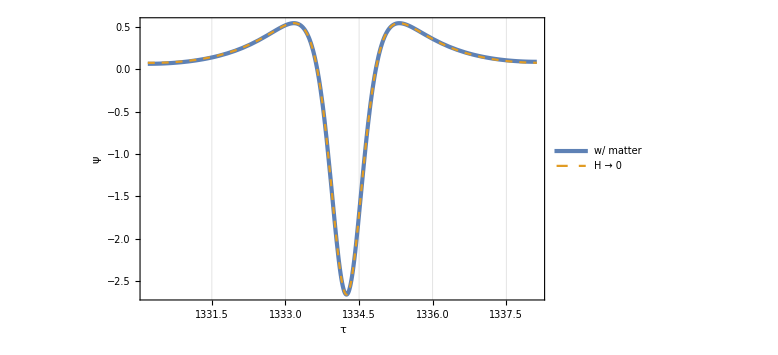

```mathematica
is=10;
Plot[{-(Vppsol[tp/mth]/mth^2-VppMeanList[[is]])/Sqrt[2VppVarList[[is]]],psi[π(tp-mth txzero[[is+1]]+1/2 dT)/dT]/.{x0->(Abs[xsol[txmax[[is]]]]+Abs[xsol[txmax[[is+1]]]])/(2f)}},{tp,mth txmax[[is]],mth txmax[[is+1]]},PlotRange->Full,GridLines->{txzero,None},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{ψ,None},{τ,n==is}},PlotLegends->Placed[{"w/ matter","H → 0"},{0.2,0.2}],ImagePadding->pad]
```

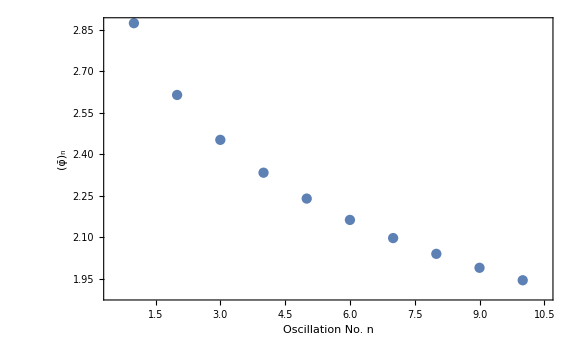

```mathematica
ListPlot[Table[{i,(Abs[xsol[txmax[[i]]]]+Abs[xsol[txmax[[i+1]]]])/(2f)},{i,1,10}],Joined->False,PlotRange->{{0.5,10.5},Full},FrameLabel->{"Oscillation No. n",Subscript[OverBar[φ], n]}]
```

```mathematica
((1+zsol[txmax[[1]]])/(1+zsol[txmax[[1+1]]]))^(3/2)
```

1.0216481682459796712667228629

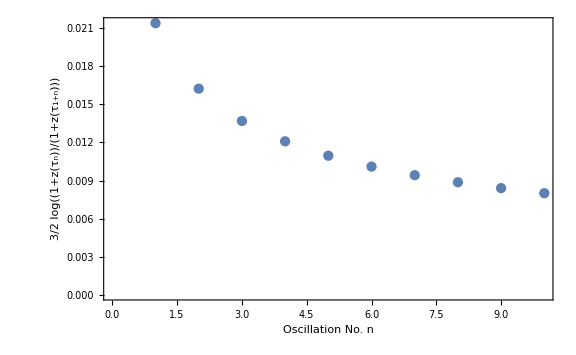

```mathematica
ListPlot[Table[{i,Log[((1+zsol[txmax[[i]]])/(1+zsol[txmax[[i+1]]]))^(3/2)]},{i,1,10}],Joined->False,FrameLabel->{"Oscillation No. n",3/2 Log[(1+z[Subscript[τ, n]])/(1+z[Subscript[τ, n+1]])]}]
```

```mathematica
mth dTList[[1]]
(Abs[xsol[txmax[[1]]]]+Abs[xsol[txmax[[2]]]])/(2f)
dT/.{x0->(Abs[xsol[txmax[[1]]]]+Abs[xsol[txmax[[2]]]])/(2f)}
((dT/.{x0->xsol[txmax[[1]]]/f})+(dT/.{x0->xsol[txmax[[2]]]/f}))/2
```

20.0754

2.8771969638389298497350169303

19.79382252366806910383453385

20.061822371782902542011171064

```mathematica
dT
```

(π Cosh[x0])/(√2)

### perturbation

```mathematica
ti=0(*t/.FindRoot[zsol[t]==9,{t,t0/100},WorkingPrecision->30]*)
```

0

```mathematica
ks=10^-3;
ptbsol=NDSolve[{dx''[t]+3Hsol[t]dx'[t]+(k^2 mth^2(1+zsol[t])^2+Vppsol[t])dx[t]==0,
dx[ti]==(1+zsol[ti])/Sqrt[2k mth],dx'[ti]==-I k mth(1+zsol[ti])dx[ti]}/.{k->ks},dx[t],{t,ti,tf},WorkingPrecision->30,MaxSteps->10^5][[1]];
```

NDSolve::precw: The precision of the differential equation ({{dx[t] (1.95497 Power[10, 6] Power[<<2>>] + <<2>>) + <<2>> == 0, <<2>>}, {}, {}, {}, {}}) is less than WorkingPrecision (30.).

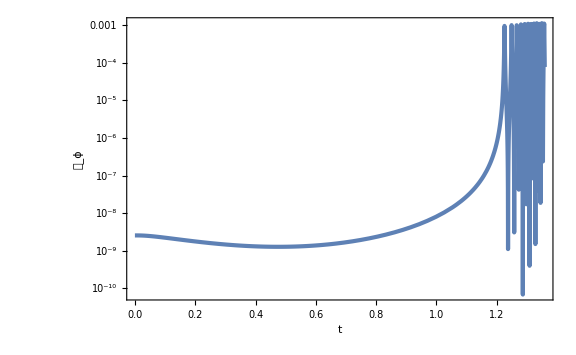

```mathematica
LogPlot[ks^3/(2 π^2)Abs[dx[t]]^2/.ptbsol,{t,ti,t0},PlotRange->Full,FrameLabel->{{Subscript[𝒫, ϕ],None},{t,k==10^-3}}]
```

```mathematica
ptbsolList[t_]=ParallelTable[k=10^lnk;{k,dx[t]/.NDSolve[{dx''[t]+3Hsol[t]dx'[t]+(k^2 mth^2(1+zsol[t])^2+Vppsol[t])dx[t]==0,
dx[ti]==(1+zsol[ti])/Sqrt[2k mth],dx'[ti]==-I k mth(1+zsol[ti])dx[ti]},dx[t],{t,ti,tf},WorkingPrecision->30,MaxSteps->10^5][[1]]//Quiet},{lnk,-4,0,10^-2}];//AbsoluteTiming
```

{2272.42,Null}

```mathematica
Export["ptbsol.wdx",ptbsolList];
```

```mathematica
ptbsolList[t_]=Import["ptbsol.wdx"][t];
```

```mathematica
calPList[t_]=Map[{#[[1]],(#[[1]]mth)^3/(2 π^2 mth^2)Abs[#[[2]]]^2}&,ptbsolList[t]];
```

```mathematica
t0 660
```

897.190041976347412577968442409

```mathematica
dt=20/660;
te=900/660;
Nt=Floor[(te-ti)/dt]
```

45

```mathematica
mth t0
```

1343.99

```mathematica
t0lat=899/660;
```

```mathematica
ticksL=Join[Table[{10^i,Superscript[10,i],0.01},{i,-10,30,10}],Flatten[Table[{10^(i+j),"",0.005},{i,1,9},{j,-20,30,10}],1]];
ticksR=Join[Table[{10^i,"",0.01},{i,-10,30,10}],Flatten[Table[{10^(i+j),"",0.005},{i,1,9},{j,-20,30,10}],1]];
```

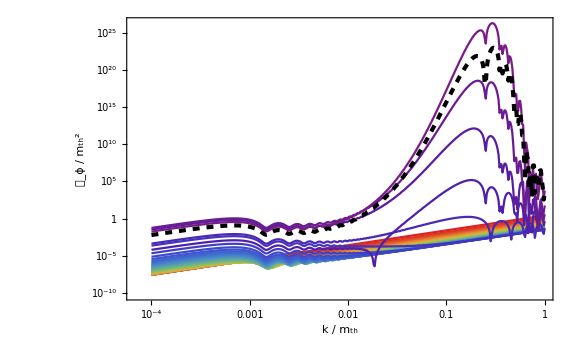

```mathematica
(*dt=10/mth;*)
(*Nt=15;*)
Show[ListLogLogPlot[Table[calPList[t],{t,(*t0-Nt dt*)ti,te,dt}],FrameLabel->{{"𝒫_ϕ / m_th^2",None},{"k / m_th","t = 20 / (660H_*)"(*"Δt = 10 / m_th"*)}},PlotStyle->Table[ColorData["Rainbow"][1-i/Nt],{i,0,Nt}],ImagePadding->padFP,FrameTicks->{{ticksL,ticksR},Automatic}],
ListLogLogPlot[calPList[t0],PlotStyle->{Black,Dashed,AbsoluteThickness[3]}]]
```

```mathematica
zsol[t0]
```

-2.58373340494×10^-17

```mathematica
Hsol[t0lat]
(ρm0(1+zsol[t0lat])^3)/(3 Hsol[t0lat]^2)
```

0.668133

0.309914

```mathematica
660t0
```

896.521920886871047490717947814

```mathematica
2 10^(-33-9)1000//N
```

2.×10^-39

```mathematica
1/(4 π^2)//N
```

0.0253303